```mathematica
ClearAll["Global`*"]
```

```mathematica
(*fluence normalized by 10^20*)
Y08Nd04:={{3.77,0.660214},{7.5,0.144152},{1.13*10,0}}
Y10Nd02:={{0.952,1.372323},{1.89,2.093081},{3.77,1.216639},{7.5,0.527595},{11.2,0.343081}}
Y065Gd065:={{2.36,2.2153},{4.7095,1.5220},{7.0310,1.2646},{9.3798,0.89512}}
Y10Tm02:={{3.7727,0.92003},{7.4926,0.93249},{11.226,0.15614},{15,0.052356}}
Y06Ho06:={{0.94884,3.0373},{1.8856,2.4976},{3.7727,2.5682},{7.5062,1.6092},{11.226,0.75397}}
Y10Nd02Zr005:={{3.7727,0.88267},{7.5062,0.50488},{11.226,0.15614},{15,0.023295}}
Y10Tm02Zr005:={{0.94884,1.2148},{1.8992,1.0986},{3.7591,0.43845},{7.5062,0.38448},{11.226,0.0659}}
Y12Zr005:={{0.94884,1.2480},{1.8856,0.44675},{3.7727,0.098023},{7.5062,0.03575}}
Y10Ho02Zr005:={{0.94884,1.9247},{1.8856,1.6964},{3.7727,1.5801},{7.5062,0.73321},{11.240,0.2890}}
```

```mathematica
phif[x_,d_,n_]:=d*x^n
f[ϕ_,c_]:=(1-ϕ+Log[ϕ])/Log[ϕ]*(1+c*ϕ)
F[fL_,fL0_,c_,n_,d_]:=f[phif[fL/fL0,d,n],c]
```

```mathematica
Manipulate[{Plot[Min[1,phif[fL/fL0,d,n]],{fL,0,10}],Plot[{f[ϕ,c],1},{ϕ,0,1},PlotRange->{0,2},PlotLegends->{"Original","1"}]},{{c,10},0,100},{{n,1.346},0,2},{{d,0.9},0,1.5},{{fL0,7},0,10}]
```

```mathematica
Manipulate[{Plot[{F[fL,fL0,c,n,d],1},{fL,0,20},PlotRange->{0,2},PlotLegends->{"Original","1"}]},{{c,10},0,100},{{n,1.346},0,3},{{d,1.1},0,1.5},{{fL0,7},0,10}]
```

```mathematica
(*Y08Nd04*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Y08Nd04
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0&&c1>0&&c1<20},{c1,d1}]
(*fL02=fL01/.Soln[[2]]*)
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n,d]},{fL,0,10},PlotRange->{0,3.2},Epilog->{PointSize[Medium],Point[{{Y08Nd04[[1,1]],Y08Nd04[[1,2]]},{(Y08Nd04[[2,1]]),Y08Nd04[[2,2]]}, {(Y08Nd04[[3,1]]),Y08Nd04[[3,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{3.77,0.660214},{7.5,0.144152},{11.3,0}}

{0.0195285,{c1→4.12479,d1→0.871823}}

4.12479

0.871823

```mathematica
(*Y10Nd02*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Y10Nd02
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.1&&c1>0&&c1<20},{c1,d1}]
(*fL02=fL01/.Soln[[2]]*)
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n1,d]},{fL,0,20},PlotRange->{0,3.2},Epilog->{PointSize[Medium],Point[{{Y10Nd02[[1,1]],Y10Nd02[[1,2]]},{(Y10Nd02[[2,1]]),Y10Nd02[[2,2]]}, {(Y10Nd02[[3,1]]),Y10Nd02[[3,2]]}, {(Y10Nd02[[4,1]]),Y10Nd02[[4,2]]}, {(Y10Nd02[[5,1]]),Y10Nd02[[5,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{0.952,1.37232},{1.89,2.09308},{3.77,1.21664},{7.5,0.527595},{11.2,0.343081}}

{0.425467,{c1→9.69136,d1→0.820415}}

9.69136

0.820415

```mathematica
(*Y065Gd065*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Y065Gd065
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.1&&c1<20&&c1>0},{c1,d1}]
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n,d]},{fL,0,20},PlotRange->{0,4.2},Epilog->{PointSize[Medium],Point[{{Y065Gd065[[1,1]],Y065Gd065[[1,2]]},{(Y065Gd065[[2,1]]),Y065Gd065[[2,2]]}, {(Y065Gd065[[3,1]]),Y065Gd065[[3,2]]}, {(Y065Gd065[[4,1]]),Y065Gd065[[4,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{2.36,2.2153},{4.7095,1.522},{7.031,1.2646},{9.3798,0.89512}}

{0.0477229,{c1→13.6356,d1→0.792876}}

13.6356

0.792876

```mathematica
(*Y10Tm02*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Y10Tm02
n=0.33318
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.1&&c1<20&&c1>0},{c1,d1}]
(*fL02=fL01/.Soln[[2]]*)
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n1,d]},{fL,0,20},PlotRange->{0,4.2},Epilog->{PointSize[Medium],Point[{{Y10Tm02[[1,1]],Y10Tm02[[1,2]]},{(Y10Tm02[[2,1]]),Y10Tm02[[2,2]]}, {(Y10Tm02[[3,1]]),Y10Tm02[[3,2]]}, {(Y10Tm02[[4,1]]),Y10Tm02[[4,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{3.7727,0.92003},{7.4926,0.93249},{11.226,0.15614},{15,0.052356}}

0.33318

{0.111964,{c1→6.60204,d1→0.77228}}

6.60204

0.77228

```mathematica
(*Y06Ho06*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Y06Ho06
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.1&&c1<20&&c1>0},{c1,d1}]
(*fL02=fL01/.Soln[[2]]*)
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n1,d]},{fL,0,20},PlotRange->{0,4.2},Epilog->{PointSize[Medium],Point[{{Y06Ho06[[1,1]],Y06Ho06[[1,2]]},{(Y06Ho06[[2,1]]),Y06Ho06[[2,2]]}, {(Y06Ho06[[3,1]]),Y06Ho06[[3,2]]}, {(Y06Ho06[[4,1]]),Y06Ho06[[4,2]]},{Y06Ho06[[5,1]],Y06Ho06[[5,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{0.94884,3.0373},{1.8856,2.4976},{3.7727,2.5682},{7.5062,1.6092},{11.226,0.75397}}

{0.139026,{c1→18.1062,d1→0.781541}}

18.1062

0.781541

```mathematica
(*Y10Nd02Zr005*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Y10Nd02Zr005
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.1&&c1<20&&c1>0},{c1,n1,d1}]
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n1,d]},{fL,0,20},PlotRange->{0,4.2},Epilog->{PointSize[Medium],Point[{{Y10Nd02Zr005[[1,1]],Y10Nd02Zr005[[1,2]]},{(Y10Nd02Zr005[[2,1]]),Y10Nd02Zr005[[2,2]]}, {(Y10Nd02Zr005[[3,1]]),Y10Nd02Zr005[[3,2]]}, {(Y10Nd02Zr005[[4,1]]),Y10Nd02Zr005[[4,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{3.7727,0.88267},{7.5062,0.50488},{11.226,0.15614},{15,0.023295}}

{0.0128012,{c1→5.22147,n1→0.451607,d1→0.785738}}

5.22147

0.785738

```mathematica
(*Y10Tm02Zr005*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
Y10Tm02Zr005
data=Drop[Y10Tm02Zr005,{-3}](*dropping the 3rd element as we suspect it could be an error.*)
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.3&&c1<20&&c1>0},{c1,d1}]
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n1,d]},{fL,0,20},PlotRange->{0,4.2},Epilog->{PointSize[Medium],Point[{{Y10Tm02Zr005[[1,1]],Y10Tm02Zr005[[1,2]]},{(Y10Tm02Zr005[[2,1]]),Y10Tm02Zr005[[2,2]]}, {(Y10Tm02Zr005[[3,1]]),Y10Tm02Zr005[[3,2]]}, {(Y10Tm02Zr005[[4,1]]),Y10Tm02Zr005[[4,2]]}, {(Y10Tm02Zr005[[5,1]]),Y10Tm02Zr005[[5,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{0.94884,1.2148},{1.8992,1.0986},{3.7591,0.43845},{7.5062,0.38448},{11.226,0.0659}}

{{0.94884,1.2148},{1.8992,1.0986},{7.5062,0.38448},{11.226,0.0659}}

{0.00439353,{c1→6.24714,d1→0.847272}}

6.24714

0.847272

```mathematica
(*Y12Zr005*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Drop[Y12Zr005,0]
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.1&&c1<20&&c1>0.1},{c1,d1}]
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n1,d]},{fL,0,20},PlotRange->{0,4.2},Epilog->{PointSize[Medium],Point[{{Y12Zr005[[1,1]],Y12Zr005[[1,2]]},{(Y12Zr005[[2,1]]),Y12Zr005[[2,2]]}, {(Y12Zr005[[3,1]]),Y12Zr005[[3,2]]}, {(Y12Zr005[[4,1]]),Y12Zr005[[4,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{0.94884,1.248},{1.8856,0.44675},{3.7727,0.098023},{7.5062,0.03575}}

{0.331072,{c1→4.30763,d1→1.02918}}

4.30763

1.02918

```mathematica
(*Y10Ho02Zr005*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,c2,d2,n2,fL01,data,Ef,xmax]
data=Y10Ho02Zr005
n=0.33318;
Ef[fL0_,c_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,d1],d1>0.1&&c1<20&&c1>0},{c1,d1}]
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
Manipulate[Plot[{F[fL,fL0,c,n1,d]},{fL,0,20},PlotRange->{0,4.2},Epilog->{PointSize[Medium],Point[{{Y10Ho02Zr005[[1,1]],Y10Ho02Zr005[[1,2]]},{(Y10Ho02Zr005[[2,1]]),Y10Ho02Zr005[[2,2]]}, {(Y10Ho02Zr005[[3,1]]),Y10Ho02Zr005[[3,2]]}, {(Y10Ho02Zr005[[4,1]]),Y10Ho02Zr005[[4,2]]},{Y10Ho02Zr005[[5,1]],Y10Ho02Zr005[[5,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n1,n},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{0.94884,1.9247},{1.8856,1.6964},{3.7727,1.5801},{7.5062,0.73321},{11.24,0.289}}

{0.0357199,{c1→11.0593,d1→0.820427}}

11.0593

0.820427

```mathematica
(*Interpolating the material parameters*)
Clear[c1,c2,d1,d2,x1,x2,c,d]
c1=15.2579;
d1=0.769;
x1=0.0;
c2=18.1062;
d2=0.781541;
x2=0.6;
c[x_]:=c1+(c2-c1)/(x2-x1)*(x-x1)
d[x_]:=d1+(d2-d1)/(x2-x1)*(x-x1)
```

15.2579

0.769

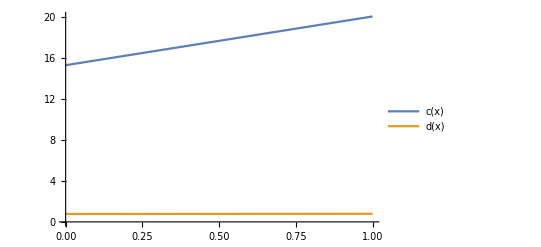

```mathematica
c[0]
d[0]
Plot[{c[x],d[x]},{x,0,1},PlotLegends->{"c(x)","d(x)"}]
```

```mathematica
(*Effect of Zr doping on Subscript[Y, 1] Subscript[Nd, 0.2]. ∆{c,d}=(w/Zr-w/0zr)/%Zr*)
(5.22147-9.69136)/0.05
(0.785738-0.820415)/0.05
```

-89.3978

-0.69354

```mathematica
(*Effect of Zr doping on Subscript[Y, 1] Subscript[Tm, 0.2]. ∆{c,d}=(w/Zr-w/0zr)/%Zr*)
(5.42415-6.60204)/0.05
(0.857641-0.77228)/0.05
```

-23.5578

1.70722

```mathematica
(*Effect of Zr doping on Subscript[Y, 1.2]. ∆{c,d}=(w/Zr-w/0zr)/%Zr*)
(6.97843-15.2579)/0.05
(1.22717-0.769007)/0.05
(*w/0 dropping last term*)
(4.30763-15.2579)/0.05
(1.02918-0.769007)/0.05
```

-165.589

9.16326

-219.005

5.20346

```mathematica
(*Comparing the theoretical Y1.2 with *)
data1=Prepend[Y08Nd04,{0,1}];
data2=Prepend[Y10Nd02,{0,1}];
data3=Prepend[Y065Gd065,{0,1}];
data4=Prepend[Y10Tm02,{0,1}];
data5=Prepend[Y06Ho06,{0,1}];
data6=Prepend[Y10Nd02Zr005,{0,1}];
data7=Prepend[Y10Tm02Zr005,{0,1}];
(*data8,data9 defined but not used below*)

n=0.33318;c=15.2579;d=0.769007;fL01=7;

dataSets={data1,data2,data3,data4,data5,data6,data7};
labels={"Y08Nd04","Y10Nd02","Y065Gd065","Y10Tm02","Y06Ho06","Y10Nd02Zr005","Y10Tm02Zr005"};
cols=ColorData[97,"ColorList"][[;;Length[dataSets]]];

(*x-range from data if you want to use it*)
{xmin,xmax}=Through[{Min,Max}[Flatten[dataSets[[All,All,1]]]]];

Manipulate[Show[Legended[ListPlot[dataSets,PlotStyle->cols,PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"x","y"}],Placed[PointLegend[cols,labels,LegendMarkers->Automatic,LabelStyle->12],{Right,Center}]],Plot[{F[fL,fL0,c1,n1,d1]},{fL,0,20},PlotRange->{0,4.2},PlotStyle->{Thick,Black}],ImageSize->Large,Background->White],{{c1,c},0,20},{{n1,n},0,2},{{d1,d},0,10},{{fL0,fL01},0,20}]
```